```mathematica
(*First：对函数f(x)=-2+sin1.5x，取不同初值进行迭代。*)
```

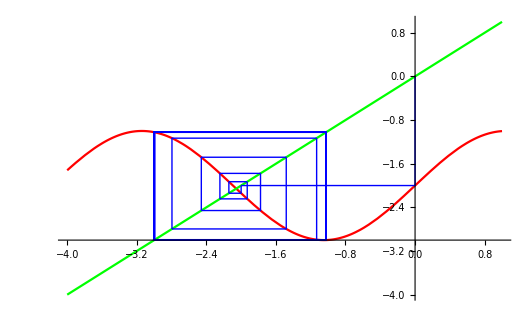

```mathematica
f[x_]:=-2+Sin[1.5 x];
f1=Plot[f[x],{x,-4,1},PlotStyle->RGBColor[1,0,0]];
f2=Plot[x,{x,-4,1},PlotStyle->RGBColor[0,1,0]];
x0=0;r={};
r0=Graphics[{RGBColor[0,0,1],Line[{{x0,0},{x0,x0}}]}];
For[i=1,i<100,i++,r=Append[r,Graphics[{RGBColor[0,0,1],Line[{{x0,x0},{x0,f[x0]},{f[x0],f[x0]}}]}]];x0=f[x0]];
Show[f1,f2,r,r0,PlotRange->{-4,1}]
```

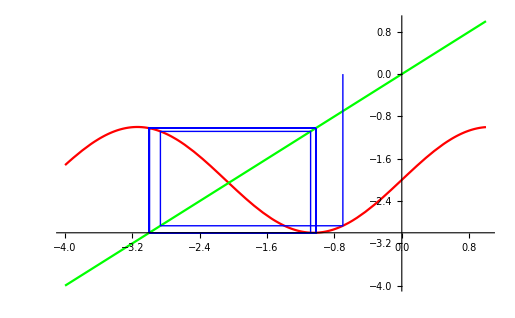

```mathematica
x0=-0.7;r={};
r0=Graphics[{RGBColor[0,0,1],Line[{{x0,0},{x0,x0}}]}];
For[i=1,i<100,i++,r=Append[r,Graphics[{RGBColor[0,0,1],Line[{{x0,x0},{x0,f[x0]},{f[x0],f[x0]}}]}]];x0=f[x0]];
Show[f1,f2,r,r0,PlotRange->{-4,1}]
```

```mathematica
(*Second：对Logistic映射取不同α观察其迭代收敛情况*)
```

{0.2,0.464,0.721242,0.583051,0.704997,0.603131,0.694156,0.61568,0.686192,0.624464,0.680075,0.630961,0.675262,0.635921,0.671424,0.63978,0.668338,0.64282,0.665847,0.645235,0.66383,0.647163,0.662194,0.64871,0.660868,0.649952,0.659791,0.650954,0.658918,0.651761,0.658209,0.652413,0.657634,0.652939,0.657168,0.653365,0.65679,0.653709,0.656483,0.653988,0.656234,0.654213,0.656033,0.654396,0.65587,0.654544,0.655737,0.654663,0.65563,0.65476}

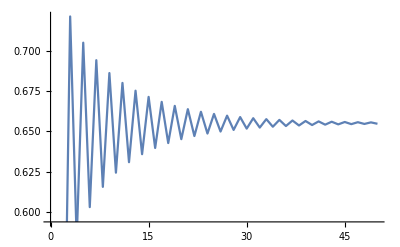

```mathematica
xn={0.2};r=2.9;
For[i=1,i<50,i++,xn=Append[xn,r*xn[[i]]*(1-xn[[i]])];]
xn
ListPlot[xn,PlotJoined->True]
```

{0.2,0.544,0.843418,0.449019,0.841163,0.454266,0.842889,0.450253,0.841586,0.453285,0.84258,0.450972,0.841827,0.452724,0.842401,0.451389,0.841966,0.452402,0.842297,0.451631,0.842046,0.452216,0.842237,0.451771,0.842092,0.452109,0.842202,0.451852,0.842118,0.452048,0.842182,0.451899,0.842133,0.452012,0.84217,0.451926,0.842142,0.451991,0.842164,0.451942,0.842147,0.451979,0.84216,0.451951,0.84215,0.451973,0.842157,0.451956,0.842152,0.451969}

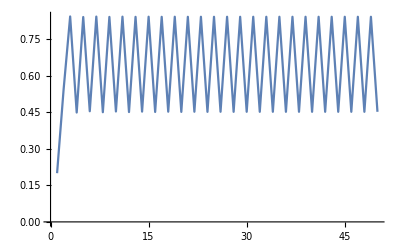

```mathematica
xn={0.2};r=3.4;
For[i=1,i<50,i++,xn=Append[xn,r*xn[[i]]*(1-xn[[i]])];]
xn
ListPlot[xn,PlotJoined->True]
```

{0.2,0.56,0.8624,0.415332,0.84991,0.446472,0.864971,0.408785,0.84588,0.456285,0.868312,0.400213,0.840149,0.470046,0.87186,0.391022,0.833433,0.485879,0.874302,0.384643,0.828425,0.49748,0.874978,0.382871,0.826983,0.500788,0.874998,0.382818,0.826939,0.500887,0.874997,0.38282,0.826941,0.500884,0.874997,0.38282,0.826941,0.500884,0.874997,0.38282,0.826941,0.500884,0.874997,0.38282,0.826941,0.500884,0.874997,0.38282,0.826941,0.500884}

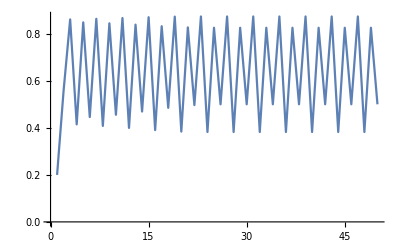

```mathematica
xn={0.2};r=3.5;
For[i=1,i<50,i++,xn=Append[xn,r*xn[[i]]*(1-xn[[i]])];]
xn
ListPlot[xn,PlotJoined->True]
```

{0.2,0.592,0.893683,0.35155,0.843462,0.488526,0.924513,0.258219,0.708704,0.763837,0.667443,0.821262,0.543125,0.918119,0.278153,0.742901,0.706697,0.766923,0.661383,0.828635,0.525396,0.922614,0.264172,0.719224,0.74718,0.698937,0.778569,0.637877,0.854663,0.459593,0.918959,0.275552,0.738606,0.714349,0.755001,0.684406,0.79918,0.593818,0.892433,0.355186,0.847406,0.478442,0.923281,0.262084,0.715566,0.753066,0.688043,0.794168,0.604822,0.884346}

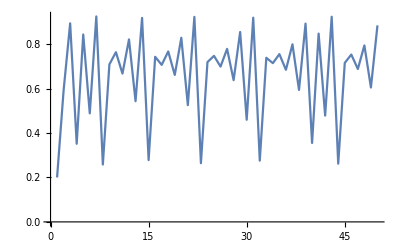

```mathematica
xn={0.2};r=3.7;
For[i=1,i<50,i++,xn=Append[xn,r*xn[[i]]*(1-xn[[i]])];]
xn
ListPlot[xn,PlotJoined->True]
```

```mathematica
(*Third：绘制Second中四个Logistic映射的蛛网图。*)
```

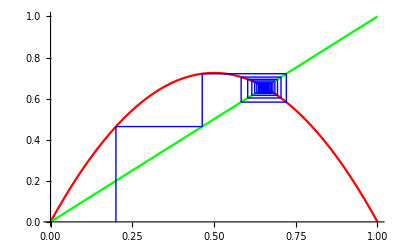

```mathematica
u=2.9;
g[x_]:=u x(1-x);
g1=Plot[g[x],{x,0,1},PlotStyle->RGBColor[1,0,0]];
g2=Plot[x,{x,0,1},PlotStyle->RGBColor[0,1,0]];
x0=0.2;r={};
r0=Graphics[{RGBColor[0,0,1],Line[{{x0,0},{x0,x0}}]}];
For[i=1,i<100,i++,r=Append[r,Graphics[{RGBColor[0,0,1],Line[{{x0,x0},{x0,g[x0]},{g[x0],g[x0]}}]}]];x0=g[x0]];
Show[g1,g2,r,r0,PlotRange->{0,1}]
```

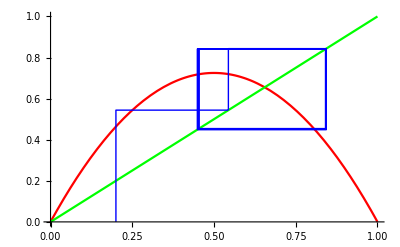

```mathematica
u=3.4;
x0=0.2;r={};
r0=Graphics[{RGBColor[0,0,1],Line[{{x0,0},{x0,x0}}]}];
For[i=1,i<100,i++,r=Append[r,Graphics[{RGBColor[0,0,1],Line[{{x0,x0},{x0,g[x0]},{g[x0],g[x0]}}]}]];x0=g[x0]];
Show[g1,g2,r,r0,PlotRange->{0,1}]
```

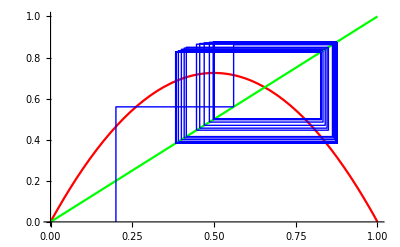

```mathematica
u=3.5;
x0=0.2;r={};
r0=Graphics[{RGBColor[0,0,1],Line[{{x0,0},{x0,x0}}]}];
For[i=1,i<100,i++,r=Append[r,Graphics[{RGBColor[0,0,1],Line[{{x0,x0},{x0,g[x0]},{g[x0],g[x0]}}]}]];x0=g[x0]];
Show[g1,g2,r,r0,PlotRange->{0,1}]
```

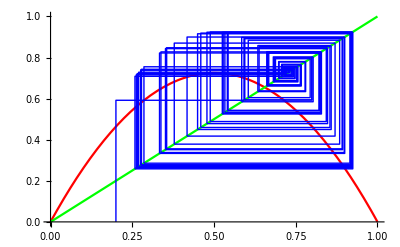

```mathematica
u=3.7;
x0=0.2;r={};
r0=Graphics[{RGBColor[0,0,1],Line[{{x0,0},{x0,x0}}]}];
For[i=1,i<100,i++,r=Append[r,Graphics[{RGBColor[0,0,1],Line[{{x0,x0},{x0,g[x0]},{g[x0],g[x0]}}]}]];x0=g[x0]];
Show[g1,g2,r,r0,PlotRange->{0,1}]
```

```mathematica
(*Forth：绘制α=4时，分别取不同的差别不大的初值的Logistic映射图。*)
```

{0.1,0.36,0.9216,0.289014,0.821939,0.585421,0.970813,0.113339,0.401974,0.961563,0.147837,0.503924,0.999938,0.000246305,0.000984976,0.00393603,0.0156821,0.0617448,0.23173,0.712124,0.820014,0.590364,0.967337,0.126384,0.441645,0.986379,0.053742,0.203415,0.64815,0.912207,0.320342,0.870893,0.449754,0.989902,0.039986,0.153548,0.519885,0.998418,0.00631654,0.0251066,0.0979049,0.353278,0.913891,0.314778,0.862771,0.473588,0.99721,0.0111304,0.0440261,0.168351,0.560037}

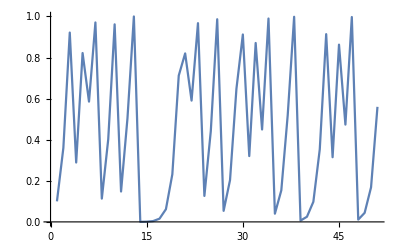

```mathematica
xn={0.1};r=4;
For[i=1,i<=50,i++,xn=Append[xn,r*xn[[i]]*(1-xn[[i]])];]
xn
ListPlot[xn,PlotJoined->True]
```

{0.1,0.36,0.9216,0.289013,0.821937,0.585426,0.97081,0.113353,0.402016,0.961596,0.147715,0.503582,0.999949,0.000205318,0.000821103,0.00328172,0.0130838,0.0516504,0.195931,0.630167,0.932226,0.252722,0.755415,0.739052,0.771416,0.705333,0.831353,0.560822,0.985203,0.0583125,0.219649,0.685612,0.862192,0.475267,0.997553,0.00976397,0.0386745,0.148715,0.506396,0.999836,0.000654488,0.00261624,0.0104376,0.0413145,0.158431,0.533321,0.995559,0.0176859,0.0694925,0.258653,0.767007}

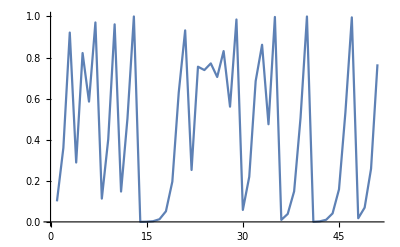

```mathematica
xn={0.1000001};r=4;
For[i=1,i<=50,i++,xn=Append[xn,r*xn[[i]]*(1-xn[[i]])];]
xn
ListPlot[xn,PlotJoined->True]
```

{0.1,0.36,0.9216,0.289014,0.821939,0.585421,0.970813,0.113341,0.401978,0.961567,0.147824,0.50389,0.999939,0.000242038,0.000967919,0.00386793,0.0154119,0.0606974,0.228053,0.704179,0.833244,0.555795,0.987548,0.0491887,0.187077,0.608316,0.95307,0.178909,0.587603,0.969303,0.119018,0.419411,0.974022,0.101214,0.363879,0.925885,0.274489,0.79658,0.648161,0.912193,0.320388,0.870958,0.44956,0.989823,0.040293,0.154678,0.523011,0.997882,0.00845385,0.0335295,0.129621}

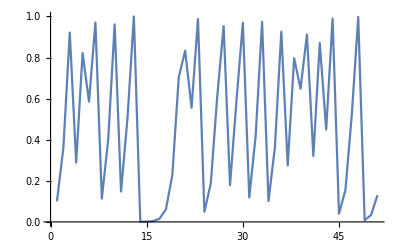

```mathematica
xn={0.10000001};r=4;
For[i=1,i<=50,i++,xn=Append[xn,r*xn[[i]]*(1-xn[[i]])];]
xn
ListPlot[xn,PlotJoined->True]
```

{0.1,0.36,0.9216,0.289014,0.821939,0.585421,0.970813,0.113339,0.401974,0.961564,0.147836,0.503923,0.999938,0.000246262,0.000984805,0.00393534,0.0156794,0.0617343,0.231693,0.712045,0.820148,0.590021,0.967585,0.125457,0.438869,0.985052,0.0588977,0.221715,0.69023,0.85525,0.49519,0.999907,0.000370115,0.00147991,0.00591089,0.0235038,0.0918054,0.333509,0.889123,0.394334,0.955339,0.170666,0.566157,0.982493,0.0688011,0.25627,0.762383,0.724621,0.798182,0.644349,0.916654}

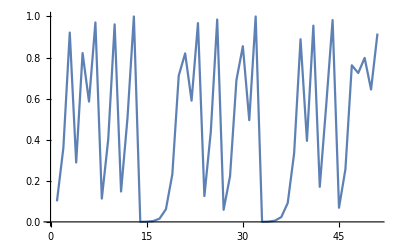

```mathematica
xn={0.1000000001};r=4;
For[i=1,i<=50,i++,xn=Append[xn,r*xn[[i]]*(1-xn[[i]])];]
xn
ListPlot[xn,PlotJoined->True]
```

```mathematica
(*Fifth：绘制Logistic的Feignbaum图。*)
```

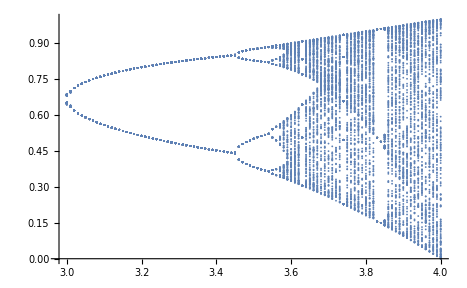

```mathematica
h[t_,x_]:=t*x*(1-x);
x0=0.5;r={};
Do[For[i=1,i≤300,i++,x0=h[t,x0];If[i>100,r=Append[r,{t,x0}]]],{t,3.0,4.0,0.01}];
ListPlot[r]
```

0.354367

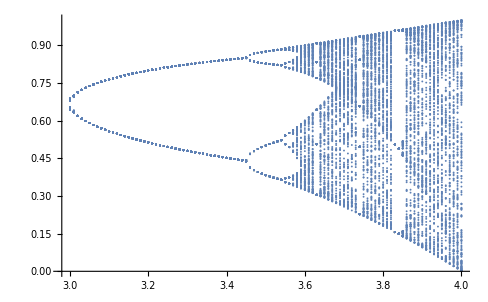

```mathematica
x0=RandomReal[{0,1}];r={};
Do[For[i=1,i≤300,i++,x0=h[t,x0];If[i>100,r=Append[r,{t,x0}]]],{t,3.0,4.0,0.01}];
x0
ListPlot[r]
```